# Name - Chanderpal Roll no. - 206428 Course - B.sc physical sci. with cs Subject - Numerical Method

# BISECTION Method

### Q1. FInd the approximate root of the equation x^3+4 x^2-10=0 using bisection method

1th iteration value is :3/2

Estimated error in 1th iteration is:1/2

2th iteration value is :5/4

Estimated error in 2th iteration is:1/4

3th iteration value is :11/8

Estimated error in 3th iteration is:1/8

4th iteration value is :21/16

Estimated error in 4th iteration is:1/16

5th iteration value is :43/32

Estimated error in 5th iteration is:1/32

6th iteration value is :87/64

Estimated error in 6th iteration is:1/64

Return[175/128]

The approximate root is :1.36719

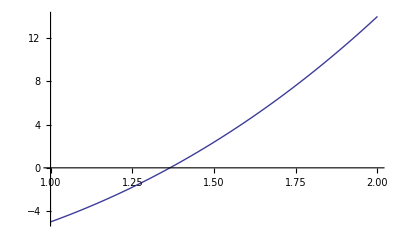

```mathematica
f[x_]:=x^3+4*x^2-10;
a=1;
b=2;
ϵ=0.01;  
Nmax=7;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial value"],
For[i=1,i≤Nmax,i++,c=(a+b)/2;
If[Abs[(b-a)/2]<ϵ,Return[c],
Print[i,"th iteration value is :",c];
Print["Estimated error in ",i,"th iteration is:",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c]]]]
Print["The approximate root is :",N[c]]
Plot[f[x],{x,1,2}]
```

### Q2. Find the approximate root of following equations using bisection method: (i) x^3-4x-9=0 (ii) cos(x) =xⅇ^x

1th iteration value is :5/2

Estimated error in 1th iteration is:1/2

2th iteration value is :11/4

Estimated error in 2th iteration is:1/4

3th iteration value is :21/8

Estimated error in 3th iteration is:1/8

4th iteration value is :43/16

Estimated error in 4th iteration is:1/16

5th iteration value is :87/32

Estimated error in 5th iteration is:1/32

6th iteration value is :173/64

Estimated error in 6th iteration is:1/64

Return[347/128]

The approximate root is :2.71094

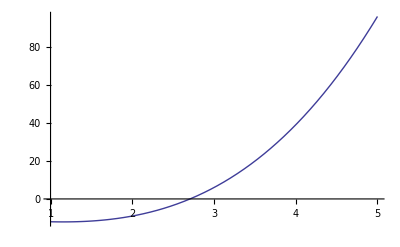

```mathematica
f[x_]:=x^3-4*x-9;
a=2;
b=3;
ϵ=0.01;
Nmax=7;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial value"],
For[i=1,i≤Nmax,i++,c=(a+b)/2;
If[Abs[(b-a)/2]<ϵ,Return[c],
Print[i,"th iteration value is :",c];
Print["Estimated error in ",i,"th iteration is:",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c]]]]
Print["The approximate root is :",N[c]]
Plot[f[x],{x,1,5}]
```

### (ii) cos(x) =xⅇ^x

1th iteration value is :1/2

Estimated error in 1th iteration is:1/2

2th iteration value is :3/4

Estimated error in 2th iteration is:1/4

3th iteration value is :5/8

Estimated error in 3th iteration is:1/8

4th iteration value is :9/16

Estimated error in 4th iteration is:1/16

5th iteration value is :17/32

Estimated error in 5th iteration is:1/32

6th iteration value is :33/64

Estimated error in 6th iteration is:1/64

Return[67/128]

The approximate root is :0.523438

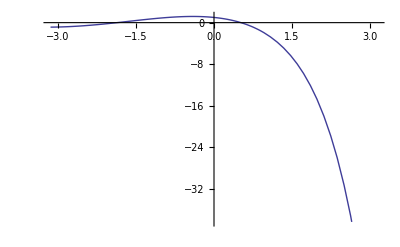

```mathematica
f[x_]:=Cos[x]-x*Exp[x];
a=0;
b=1;
ϵ=0.01;
Nmax=10;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial value"],
For[i=1,i≤Nmax,i++,c=(a+b)/2;
If[Abs[(b-a)/2]<ϵ,Return[c],
Print[i,"th iteration value is :",c];
Print["Estimated error in ",i,"th iteration is:",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c]]]]
Print["The approximate root is :",N[c]]
Plot[f[x],{x,-Pi,Pi}]
```

### (iii)Sin(x)+ⅇ^x=0

1th iteration value is :0

Estimated error in 1th iteration is:1

2th iteration value is :-1/2

Estimated error in 2th iteration is:1/2

3th iteration value is :-3/4

Estimated error in 3th iteration is:1/4

4th iteration value is :-5/8

Estimated error in 4th iteration is:1/8

5th iteration value is :-9/16

Estimated error in 5th iteration is:1/16

6th iteration value is :-19/32

Estimated error in 6th iteration is:1/32

7th iteration value is :-37/64

Estimated error in 7th iteration is:1/64

Return[-75/128]

The approximate root is :-0.585938

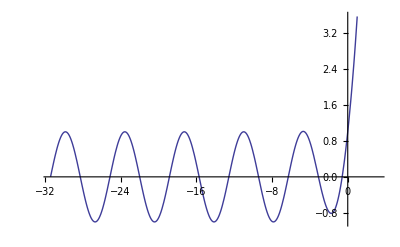

```mathematica
f[x_]:=Sin[x]+Exp[x];
a=-1;
b=1;
ϵ=0.01;
Nmax=10;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial value"],
For[i=1,i≤Nmax,i++,c=(a+b)/2;
If[Abs[(b-a)/2]<ϵ,Return[c],
Print[i,"th iteration value is :",c];
Print["Estimated error in ",i,"th iteration is:",(b-a)/2];
If[f[a]*f[c]<0,b=c,a=c]]]]
Print["The approximate root is :",N[c]]
Plot[f[x],{x,-10Pi,Pi}]
```

Secant Method

Q1. Find approximate root of the equation x^3-2x-5 = 0.

1th iteraton value is :2.05882

Estimated error is :0.941176

2th iteraton value is :2.08126

Estimated error is :0.0224401

3th iteraton value is :2.09482

Estimated error is :0.0135605

4th iteraton value is :2.09455

Estimated error is :0.000274715

5th iteraton value is :2.09455

Estimated error is :2.05019×10^-6

Return[2.09455]

Approximate root is :2.09455

Estimated error is :3.14728×10^-10

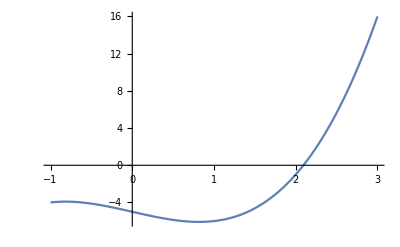

```mathematica
f[x_]:=x^3-2 x-5;
Subscript[x, 0]=2;
Subscript[x, 1]=3;
ϵ=0.000001;
Nmax=10;                  "Maximum number of iterations";
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,
   Print["These values do not satisfy the IVP so change the initial value"],
      For[n=2,n≤Nmax,n++,
          Subscript[x, n]=N[Subscript[x, n-1]-f[Subscript[x, n-1]](Subscript[x, n-1]-Subscript[x, n-2])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
        
       If[Abs[Subscript[x, n]-Subscript[x, n-1]]<ϵ,Return[Subscript[x, n]]];
         Print[n-1,"th iteraton value is :",Subscript[x, n]];
         Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]]]
         Print["Approximate root is :",Subscript[x, n]]
         Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]
Plot[f[x],{x,-1,3}]
```

# Regula falsi method

### Q1.f(x)=Cos(x)

1th iterative value is :1.41228

Estimated error is :0.587717

2th iterative value is :1.57391

Estimated error is :0.161623

3th iterative value is :1.57078

Estimated error is :0.0031228

4th iterative value is :1.5708

Estimated error is :0.0000128049

Return[1.5708]

Approximate root is : 1.5708

Estimated error is :2.05567×10^-11

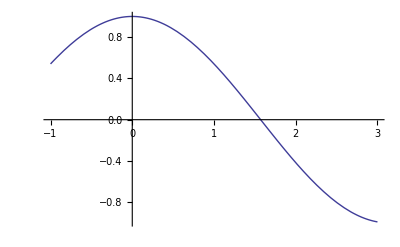

```mathematica
f[x_]:=Cos[x]
a=0;
b=2;
ϵ=0.00000001;
nmax=15;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial values"],
For[i=1,i≤nmax,i++,x=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
If[f[x]*f[b]>0,b=x,a=x];
If[Abs[b-a]<ϵ,Return[x]];
  Print[i,"th iterative value is :",N[x]];
Print["Estimated error is :",N[b-a]]]];
Print["Approximate root is : ",N[x]];
Print["Estimated error is :",N[b-a]];
Plot[f[x],{x,-1,3}]
```

### Q2. f(x)=e^-x-x

1th iterative value is :0.6127

Estimated error is :0.6127

2th iterative value is :0.572181

Estimated error is :0.572181

3th iterative value is :0.567703

Estimated error is :0.567703

4th iterative value is :0.567206

Estimated error is :0.567206

5th iterative value is :0.56715

Estimated error is :0.56715

6th iterative value is :0.567144

Estimated error is :0.567144

7th iterative value is :0.567143

Estimated error is :0.567143

8th iterative value is :0.567143

Estimated error is :0.567143

9th iterative value is :0.567143

Estimated error is :0.567143

10th iterative value is :0.567143

Estimated error is :0.567143

11th iterative value is :0.567143

Estimated error is :0.567143

12th iterative value is :0.567143

Estimated error is :0.567143

13th iterative value is :0.567143

Estimated error is :0.567143

14th iterative value is :0.567143

Estimated error is :0.567143

15th iterative value is :0.567143

Estimated error is :0.567143

16th iterative value is :0.567143

Estimated error is :0.567143

Return[0.567143]

Approximate root is : 0.567143

Estimated error is :2.22045×10^-16

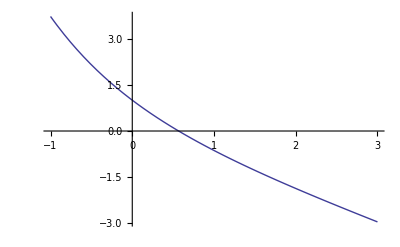

```mathematica
f[x_]:=Exp[-x]-x;
a=0;
b=1;
ϵ=0.00000001;
nmax=20;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial values"],
For[i=1,i≤nmax,i++,x=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
If[f[x]*f[b]>0,b=x,a=x];
If[Abs[b-a]<ϵ,Return[x]];
  Print[i,"th iterative value is :",N[x]];
Print["Estimated error is :",N[b-a]]]];
Print["Approximate root is : ",N[x]];
Print["Estimated error is :",N[b-a]];
Plot[f[x],{x,-1,3}]
```

### Q3.

1th iterative value is :0.486148

Estimated error is :0.0138523

2th iterative value is :0.486387

Estimated error is :0.0136127

3th iterative value is :0.486389

Estimated error is :0.013611

4th iterative value is :0.486389

Estimated error is :0.013611

5th iterative value is :0.486389

Estimated error is :0.013611

6th iterative value is :0.486389

Estimated error is :0.013611

7th iterative value is :0.486389

Estimated error is :0.013611

8th iterative value is :0.486389

Estimated error is :0.013611

9th iterative value is :0.486389

Estimated error is :0.013611

10th iterative value is :0.486389

Estimated error is :0.013611

11th iterative value is :0.486389

Estimated error is :0.013611

12th iterative value is :0.486389

Estimated error is :0.013611

13th iterative value is :0.486389

Estimated error is :0.013611

14th iterative value is :0.486389

Estimated error is :0.013611

15th iterative value is :0.486389

Estimated error is :0.013611

16th iterative value is :0.486389

Estimated error is :0.013611

17th iterative value is :0.486389

Estimated error is :0.013611

18th iterative value is :0.486389

Estimated error is :0.013611

19th iterative value is :0.486389

Estimated error is :0.013611

20th iterative value is :0.486389

Estimated error is :0.013611

Approximate root is : 0.486389

Estimated error is :0.013611

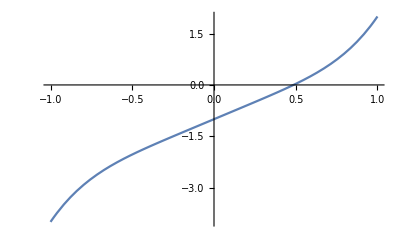

```mathematica
f[x_]:=x^5+2 x-1;
a=0.45;
b=0.5;
ϵ=0.01;
nmax=20;
If[f[a]*f[b]>0,
Print["These values do not satify the IVP so change the initial values"],
For[i=1,i≤nmax,i++,x=N[(a*f[b]-b*f[a])/(f[b]-f[a])];
If[f[x]*f[b]>0,b=x,a=x];
If[Abs[b-a]<ϵ,Return[x]];
  Print[i,"th iterative value is :",N[x]];
Print["Estimated error is :",N[b-a]]]];
Print["Approximate root is : ",N[x]];
Print["Estimated error is :",N[b-a]];
Plot[f[x],{x,-1,1}]
```

# Newton Raphson Method

### Q1.Find the approximate root of the equation x^4-x-10=0.

1th iteration value is 1.87097

Estimated error is :0.129032

2th iteration value is 1.85578

Estimated error is :0.015187

3th iteration value is 1.85558

Estimated error is :0.000196141

Return[1.85558]

The Final approximate root is 1.85558

Estimated error is:3.23699×10^-8

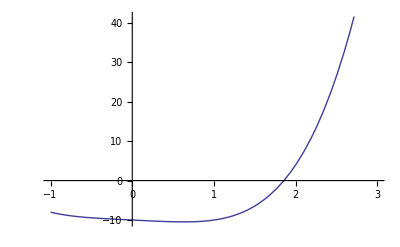

```mathematica
f[x_]:=x^4-x-10
Subscript[x, 0]=2;
ϵ=5*10^-5;
Nmax=5;
For[n=1,n≤Nmax,n++,Subscript[x, n]=N[Subscript[x, n-1]-f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<ϵ,Return[Subscript[x, n]]];
Print[n,"th iteration value is ",Subscript[x, n]];
Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["The Final approximate root is ",Subscript[x, n]];
Print["Estimated error is:",Abs[Subscript[x, n]-Subscript[x, n-1]]]
Plot[f[x],{x,-1,3}]
```

### Q2.Find approximate root of the following equations using N-R method: (i) 3x-cos(x)-1=0 (ii) e^-x=x (iii) cos(x)-xe^x=0

## (i)

1th iteration value is 0.614547

Estimated error is :1.38545

2th iteration value is 0.607108

Estimated error is :0.00743927

Return[0.607102]

The Final approximate root is 0.607102

Estimated error is:6.34307×10^-6

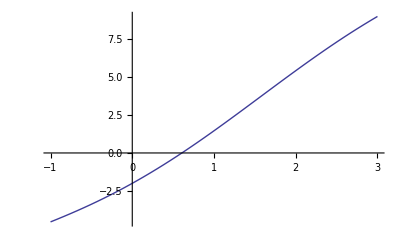

```mathematica
f[x_]:=3 x-Cos[x]-1
Subscript[x, 0]=2;
ϵ=5*10^-5;
Nmax=5;
For[n=1,n≤Nmax,n++,Subscript[x, n]=N[Subscript[x, n-1]-f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<ϵ,Return[Subscript[x, n]]];
Print[n,"th iteration value is ",Subscript[x, n]];
Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["The Final approximate root is ",Subscript[x, n]];
Print["Estimated error is:",Abs[Subscript[x, n]-Subscript[x, n-1]]]
Plot[f[x],{x,-1,3}]
```

### (ii)

```mathematica
f[x_]:=Exp[-x]-x
Subscript[x, 0]=1;
ϵ=5*10^-5;
Nmax=5;
For[n=1,n≤Nmax,n++,Subscript[x, n]=N[Subscript[x, n-1]-f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<ϵ,Return[Subscript[x, n]]];
Print[n,"th iteration value is ",Subscript[x, n]];
Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["The Final approximate root is ",Subscript[x, n]];
Print["Estimated error is:",Abs[Subscript[x, n]-Subscript[x, n-1]]]
Plot[f[x],{x,-1,3}]
```

1th iteration value is 0.537883

Estimated error is :0.462117

2th iteration value is 0.566987

Estimated error is :0.0291041

3th iteration value is 0.567143

Estimated error is :0.000156295

Return[0.567143]

The Final approximate root is 0.567143

Estimated error is:4.42066×10^-9

-Graphics-

### (iii)

1th iteration value is 0.653079

Estimated error is :0.346921

2th iteration value is 0.531343

Estimated error is :0.121736

3th iteration value is 0.51791

Estimated error is :0.0134335

4th iteration value is 0.517757

Estimated error is :0.00015253

Return[0.517757]

The Final approximate root is 0.517757

Estimated error is:1.94824×10^-8

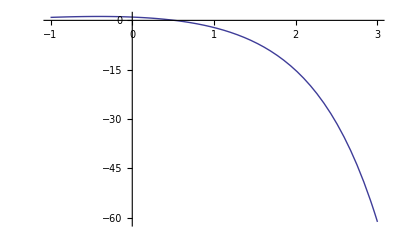

```mathematica
f[x_]:=Cos[x]-x Exp[x]
Subscript[x, 0]=1;
ϵ=5*10^-5;
Nmax=5;
For[n=1,n≤Nmax,n++,Subscript[x, n]=N[Subscript[x, n-1]-f[Subscript[x, n-1]]/f'[Subscript[x, n-1]]];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<ϵ,Return[Subscript[x, n]]];
Print[n,"th iteration value is ",Subscript[x, n]];
Print["Estimated error is :",Abs[Subscript[x, n]-Subscript[x, n-1]]]];
Print["The Final approximate root is ",Subscript[x, n]];
Print["Estimated error is:",Abs[Subscript[x, n]-Subscript[x, n-1]]]
Plot[f[x],{x,-1,3}]
```

# Gauss- Jordan Method

# Q1: Solve the given system of equations using Gauss Jordan method. y+z=2 2x+3z=5 x+y+z=3

```mathematica
Soln:A={{0,1,1,2},{2,0,3,5},{1,1,1,3}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

(0 | 1 | 1 | 2
2 | 0 | 3 | 5
1 | 1 | 1 | 3)

(1 | 0 | 0 | 1
0 | 1 | 0 | 1
0 | 0 | 1 | 1)

```mathematica
Solve[{x==1,y==1,z==1},{x,y,z}]
```

{{x→1,y→1,z→1}}

## Q2: Solve the given system of equations using Gauss Jordan method. x+y+z=9 2x-3y+4z=13 3x+4y+5z=40

```mathematica
Soln:A={{1,1,1,9},{2,-3,4,13},{3,4,5,40}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

(1 | 1 | 1 | 9
2 | -3 | 4 | 13
3 | 4 | 5 | 40)

(1 | 0 | 0 | 1
0 | 1 | 0 | 3
0 | 0 | 1 | 5)

```mathematica
Solve[{x==1,y==3,z==5},{x,y,z}]
```

{{x→1,y→3,z→5}}

## Q3: Solve the given system of equations using Gauss Jordan method. 2x-3y+z=-1 x+4y+5z=25 3x-4y+z=2

```mathematica
Soln:A={{2,-3,1,-1},{1,4,5,25},{3,-4,1,2}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

(2 | -3 | 1 | -1
1 | 4 | 5 | 25
3 | -4 | 1 | 2)

(1 | 0 | 0 | 87/10
0 | 1 | 0 | 57/10
0 | 0 | 1 | -13/10)

```mathematica
Solve[{x==87/10,y==57/10,z==-12/10},{x,y,z}]
```

{{x→87/10,y→57/10,z→-6/5}}

## Q4: Solve the given system of equations using Gauss Jordan method. x+2y+6z=22 3x+4y+z=26 6x-y-z=13

```mathematica
Soln:A={{1,2,6,22},{3,4,1,26},{6,-1,-1,13}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

(1 | 2 | 6 | 22
3 | 4 | 1 | 26
6 | -1 | -1 | 13)

(1 | 0 | 0 | 152/49
0 | 1 | 0 | 181/49
0 | 0 | 1 | 94/49)

```mathematica
Solve[{x==152/49,y==181/49,z==94/49},{x,y,z}]
```

{{x→152/49,y→181/49,z→94/49}}

## Q5: Solve the given system of equations using Gauss Jordan method. x+2y+6z=44 3x+4y+z=52 6x-y-z=30

```mathematica
Soln:A={{1,2,6,44},{3,4,1,52},{6,-1,-1,30}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

(1 | 2 | 6 | 44
3 | 4 | 1 | 52
6 | -1 | -1 | 30)

(1 | 0 | 0 | 1000/147
0 | 1 | 0 | 1018/147
0 | 0 | 1 | 572/147)

```mathematica
Solve[{x==1000/147,y==1018/147,z==572/147},{x,y,z}]
```

{{x→1000/147,y→1018/147,z→572/147}}

# Gauss- Elimination Method

# Q1- Solve the given system of equation using gauss elimination method: 2x+y+z=4 3x+5y+2z=15 2x+y+4z=18

```mathematica
A={{2,1,1},{3,5,2},{2,1,4}};
A//MatrixForm
b={4,15,8};
b//MatrixForm
m1=Length[A];
m2=Length[b];
x=Table[0,{m1}];
If[m1≠m2,Print["The system cannot be solved"],Table[AppendTo[A⟦i⟧,b⟦i⟧],{i,m1}];
Print["[A|b]=",A//MatrixForm];
For[i=1,i≤m1-1,i++,s=Abs[A⟦i,i⟧];
c=i;
For[j=i+1,j≤m1,j++,If[Abs[A⟦j,i⟧]>s,s=A⟦j,i⟧;
c=j;]];
For[k=1,k≤m1+1,k++,d[k]=A⟦i,k⟧;
A⟦i,k⟧=A⟦c,k⟧;
A⟦c,k⟧=d[k]];
Print["Step",i, A//MatrixForm];
For[j=i+1,j≤m1,j++,m=A⟦j,i⟧/A⟦i,i⟧;
For[k=1,k≤m1+1,k++,A⟦j,k⟧=A⟦j,k⟧-(m*A⟦i,k⟧)];];
Print[A//MatrixForm];];
For[i=0,i≤m1-1,i++,x⟦m1-i⟧=(A⟦m1-i,m1+1⟧-Sum[A⟦m1-i,j⟧*x⟦j⟧,{j,m1-i+1,m1}])/A⟦m1-i,m1-i⟧;];
Print["x",x//MatrixForm];]
```

(2 | 1 | 1
3 | 5 | 2
2 | 1 | 4)

(4
15
8)

[A|b]=(2 | 1 | 1 | 4
3 | 5 | 2 | 15
2 | 1 | 4 | 8)

Step1(3 | 5 | 2 | 15
2 | 1 | 1 | 4
2 | 1 | 4 | 8)

(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

Step2(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | -7/3 | 8/3 | -2)

(3 | 5 | 2 | 15
0 | -7/3 | -1/3 | -6
0 | 0 | 3 | 4)

x(1/7
50/21
4/3)

Gauss - Jacobi Method

Q1. Find the given system of linear equations using Gauss - Jacobi Method:
(i)	27 x_1 + 6 x_2 - x_3 = 85 ,       6 x_1 + 15 x_2 + 2 x_3 = 72 ,      x_1 +  x_2 + 54 x_3 = 110  
(ii)	5 x_1 + 2 x_2 + x_3 = 10 ,       3 x_1 + 7 x_2 + 4 x_3 = 21 ,      x_1 +  x_2 + 9 x_3 = 12
(iii)	10 x_1 - 2 x_2 + x_3 = 12 ,        x_1 + 9 x_2 -  x_3 = 10 ,      2 x_1 -  x_2 + 11 x_3 = 20

(i)

```mathematica
n=3;
a={{27,6,-1},{6,15,2},{1,1,54}};
MatrixForm[a]
x={0,0,0}

b={85,72,110}
For[k=1,k≤5,k++,
   For[i=1,i≤n,i++,
y[[i]]=
     (b[[i]]-Sum[a[[i,j]]*x[[j]],{j,1,i-1}]-Sum[a[[i,j]]*x[[j]],{j,i+1,n}])/a[[i,i]]];
  For[m=1,m≤n,m++,x[[m]]=N[y[[m]]]]]
  For[p=1,p≤n,p++,Print["x[",p,"]=",x[[p]]]]
```

```mathematica
({{27, 6, -1}, {6, 15, 2}, {1, 1, 54}})B
```

{0,0,0}

{85,72,110}

x[1]=2.43155

x[2]=3.58328

x[3]=1.92692

Gauss - Seidel Method

(i)

```mathematica
n=3;
a={{27,6,-1},{6,15,2},{1,1,54}};
MatrixForm[a]
x={0,0,0}

b={85,72,110}
For[k=1,k≤5,k++,
   For[i=1,i≤n,i++,
y[[i]]=
     (b[[i]]-Sum[a[[i,j]]*y[[j]],{j,1,i-1}]-Sum[a[[i,j]]*y[[j]],{j,i+1,n}])/a[[i,i]]];
  For[m=1,m≤n,m++,x[[m]]=N[y[[m]]]]]
  For[p=1,p≤n,p++,Print["x[",p,"]=",x[[p]]]]
```

(27 | 6 | -1
6 | 15 | 2
1 | 1 | 54)

{0,0,0}

{85,72,110}

x[1]=2.42548

x[2]=3.57302

x[3]=1.92595

# Newton-Interpolation

### Q1. For the data (3,293), (5,508),(6,585),(9,764). Using newton Interpolation find interpolation polynomial p(x) and also find p(5,6).

```mathematica
points={{3,293},{5,508},{6,585},{9,764}};
n= Length[points]
y= points[[All,1]]
f= points[[All,2]]
dd[k_]:=Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}];
p[x_]= Sum[(dd[i]*Product[If[i≤j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[5.6]]
```

4

{3,5,6,9}

{293,508,585,764}

293+215/2 (-3+x)-61/6 (-5+x) (-3+x)+35/36 (-6+x) (-5+x) (-3+x)

1/36 (-9702+9003 x-856 x^2+35 x^3)

556.033

```mathematica
Q2 For the  following data find the polynomial p(x)
1.(-1,2),(0,1),(1,0),(3,-1).  Also find p(6)
```

```mathematica
points={{-1,2},{0,1},{1,0},{3,-1}};
n= Length[points]
y= points[[All,1]]
f= points[[All,2]]
dd[k_]:=Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}];
p[x_]= Sum[(dd[i]*Product[If[i≤j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[6]]
```

4

{-1,0,1,3}

{2,1,0,-1}

1-x+1/24 (-1+x) x (1+x)

1/24 (24-25 x+x^3)

15/4

## 2. (0,1),(1,3),(2,9), (3,31) , (4,81) . Also find p(3.5) and p(2.8)

```mathematica
points={{0,1},{1,3},{2,9},{3,31},{4,81}};
n= Length[points]
y= points[[All,1]]
f= points[[All,2]]
dd[k_]:=Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}];
p[x_]= Sum[(dd[i]*Product[If[i≤j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[3.5]]
Evaluate[p[2.8]]
```

5

{0,1,2,3,4}

{1,3,9,31,81}

1+2 x+2 (-1+x) x+2 (-2+x) (-1+x) x

1+4 x-4 x^2+2 x^3

51.75

24.744

## 3. (4,48),(5,100),(7,294), (10,900) , (11,1210) , (13,2028) . Also find p(8).

```mathematica
points={{4,48},{5,100},{7,294},{10,1900},{11,1210},{13,2028}};
n= Length[points]
y= points[[All,1]]
f= points[[All,2]]
dd[k_]:=Sum[(f[[i]]/Product[If[Equal[j,i],1,(y[[i]]-y[[j]])],{j,1,k}]),{i,1,k}];
p[x_]= Sum[(dd[i]*Product[If[i≤j,1,x-y[[j]]],{j,1,i-1}]),{i,1,n}]
Simplify[p[x]]
Evaluate[p[8]]
```

6

{4,5,7,10,11,13}

{48,100,294,1900,1210,2028}

48+52 (-4+x)+15 (-5+x) (-4+x)+109/9 (-7+x) (-5+x) (-4+x)-100/9 (-10+x) (-7+x) (-5+x) (-4+x)+100/27 (-11+x) (-10+x) (-7+x) (-5+x) (-4+x)

1/27 (-2002000+1522900 x-442027 x^2+61027 x^3-4000 x^4+100 x^5)

3344/3

# Lagrange Interpolation

```mathematica
Q1 For the data (-1,5),(0,1),(1,1),(2,11). Using Lagrange Interpolation polynomial p(x) and also find p(1.5).
```

```mathematica
xi={-1,0,1,2}
fi={5,1,1,11}
n= Length[xi]
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*
(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))]
p[x_]= ∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange interpolation Polynomial p[x]=",p[x]]
Print["simplify Lagrange Interpolation Polynomial p[x]=", Simplify[p[x]]]
Print["Value of f at x=1.5 is ", p[1.5]]
```

{-1,0,1,2}

{5,1,1,11}

4

Lagrange interpolation Polynomial p[x]=-5/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+1/2 (2-x) x (1+x)+11/6 (-1+x) x (1+x)

simplify Lagrange Interpolation Polynomial p[x]=1-3 x+2 x^2+x^3

Value of f at x=1.5 is 4.375

## Q2 For the following data find the polynomial p(x) 1.(-1,2), (0,1),(1,0),(3,-1). Also find p(6).

```mathematica
xi={-1,0,1,3}
fi={2,1,0,-1}
n= Length[xi]
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*
(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))]
p[x_]= ∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange interpolation Polynomial p[x]=",p[x]]
Print["simplify Lagrange Interpolation Polynomial p[x]=", Simplify[p[x]]]
Print["Value of f at x=6 is ", p[6]]
```

{-1,0,1,3}

{2,1,0,-1}

4

Lagrange interpolation Polynomial p[x]=-1/4 (1-x) (3-x) x+1/3 (1-x) (3-x) (1+x)-1/24 (-1+x) x (1+x)

simplify Lagrange Interpolation Polynomial p[x]=1/24 (24-25 x+x^3)

Value of f at x=6 is 15/4

## 2. (0,1),(1,3),(2,9), (3,31) , (4,81) . Also find p(3.5) and p(2.8)

```mathematica
xi={0,1,2,3,4}
fi={1,3,9,31,81}
n= Length[xi]
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*
(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))]
p[x_]= ∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange interpolation Polynomial p[x]=",p[x]]
Print["simplify Lagrange Interpolation Polynomial p[x]=", Simplify[p[x]]]
Print["Value of f at x=3.5 is ", p[3.5]]
Print["Value of f at x=2.8 is ", p[2.8]]
```

{0,1,2,3,4}

{1,3,9,31,81}

5

Lagrange interpolation Polynomial p[x]=1/24 (1-x) (2-x) (3-x) (4-x)+1/2 (2-x) (3-x) (4-x) x+9/4 (3-x) (4-x) (-1+x) x+31/6 (4-x) (-2+x) (-1+x) x+27/8 (-3+x) (-2+x) (-1+x) x

simplify Lagrange Interpolation Polynomial p[x]=1+4 x-4 x^2+2 x^3

Value of f at x=3.5 is 51.75

Value of f at x=2.8 is 24.744

## 3. (4,48),(5,100),(7,294), (10,900) , (11,1210) , (13,2028) . Also find p(8).

```mathematica
xi={4,5,7,10,11,13}
fi={48,100,294,900,1210,2028}
n= Length[xi]
For[k=1,k≤n,k++,
Subscript[L, k][x_]=(∏_(j=1)^(k-1) (x-xi[[j]])/(xi[[k]]-xi[[j]]))*
(∏_(j=k+1)^n (x-xi[[j]])/(xi[[k]]-xi[[j]]))]
p[x_]= ∑_(k=1)^n Subscript[L, k][x]*fi[[k]];
Print["Lagrange interpolation Polynomial p[x]=",p[x]]
Print["simplify Lagrange Interpolation Polynomial p[x]=", Simplify[p[x]]]
Print["Value of f at x=8 is ", p[8]]
```

{4,5,7,10,11,13}

{48,100,294,900,1210,2028}

6

Lagrange interpolation Polynomial p[x]=8/189 (5-x) (7-x) (10-x) (11-x) (13-x)+5/24 (7-x) (10-x) (11-x) (13-x) (-4+x)+49/72 (10-x) (11-x) (13-x) (-5+x) (-4+x)+10/3 (11-x) (13-x) (-7+x) (-5+x) (-4+x)+605/168 (13-x) (-10+x) (-7+x) (-5+x) (-4+x)+169/216 (-11+x) (-10+x) (-7+x) (-5+x) (-4+x)

simplify Lagrange Interpolation Polynomial p[x]=(-1+x) x^2

Value of f at x=8 is 448

# Trapezoidal Rule

Q 1 : Using Trapezoidal Rule to Integrate f(x) = ⅇ^(x^2) from 0 to 2 for n = 10.

```mathematica
f[x_]=Exp[x^2];
a=0;
b=2;
n=10;
h=(b-a)/n;
app=N[(h/2)*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,2}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 16.4526

The approxiamate value of f[x] is 17.1702

The error is 0.717582

Q 2 : Using Trapezoidal Rule to evaluate the following
(i)	∫_0^1 x^2/(1+x^3)ⅆx   for n=5
(ii)	∫_0^6 dx/(1+x^2)   for n=6
(iii)	∫_0^0.6 ⅇ^(-x^2)dx   for n=6

### (i)

```mathematica
f[x_]=x^2/(1+x^3);
a=0;
b=1;
n=5;
h=(b-a)/n;
app=N[(h/2)*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,1}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 0.231049

The approxiamate value of f[x] is 0.231878

The error is 0.000829247

### (ii)

```mathematica
f[x_]=1/(1+x^2);
a=0;
b=6;
n=6;
h=(b-a)/n;
app=N[(h/2)*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,6}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 1.40565

The approxiamate value of f[x] is 1.4108

The error is 0.00515093

### (iii)

```mathematica
f[x_]=Exp[-x^2];
a=0;
b=0.6;
n=6;
h=(b-a)/n;
app=N[(h/2)*(f[a]+2*Sum[f[i],{i,a+h,b-h,h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,0.6}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 0.535154

The approxiamate value of f[x] is 0.534455

The error is 0.000698207

# Simpson’s 1/3 Rule

Q 1 : Using Simpson’s 1/3 Rule to Integrate f(x) = x^2/(1+x^3) from 0 to 1 for n = 4.

```mathematica
f[x_]=x^2/(1+x^3);
a=0;
b=1;
n=4;
h=(b-a)/n;
app=N[(h/3)*(f[a]+4*Sum[f[i],{i,a+h,b-h,2 h}]+2*Sum[f[i],{i,a+2 h,b-2 h,2 h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,1}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 0.231049

The approxiamate value of f[x] is 0.231085

The error is 0.0000355959

Q 2 : Using Simpson’s 1/3 Rule to evaluate the following
(i)	∫_0^1 1/(x^2+6x+10)ⅆx   for n=10
(ii)	∫_0^6 dx/(1+x^2)   for n=6
(iii)	∫_0^0.6 ⅇ^(-x^2)dx   for n=6

### (i)

```mathematica
f[x_]=1/(x^2+6x+10);
a=0;
b=1;
n=10;
h=(b-a)/n;
app=N[(h/3)*(f[a]+4*Sum[f[i],{i,a+h,b-h,2 h}]+2*Sum[f[i],{i,a+2 h,b-2 h,2 h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,1}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 0.0767719

The approxiamate value of f[x] is 0.0767719

The error is 2.23635×10^-8

### (ii)

```mathematica
f[x_]=1/(1+x^2);
a=0;
b=6;
n=10;
h=(b-a)/n;
app=N[(h/3)*(f[a]+4*Sum[f[i],{i,a+h,b-h,2 h}]+2*Sum[f[i],{i,a+2 h,b-2 h,2 h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,6}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 1.40565

The approxiamate value of f[x] is 1.40016

The error is 0.0054858

### (iii)

```mathematica
f[x_]=Exp[-x^2];
a=0;
b=0.6;
n=6;
h=(b-a)/n;
app=N[(h/3)*(f[a]+4*Sum[f[i],{i,a+h,b-h,2 h}]+2*Sum[f[i],{i,a+2 h,b-2 h,2 h}]+f[b])];
Ex=N[Integrate[f[x],{x,0,0.6}]];
Print["The exact value of f[x] is ",Ex]
Print["The approxiamate value of f[x] is ",app]
Print["The error is ",Abs[Ex-app]]
```

The exact value of f[x] is 0.886227

The approxiamate value of f[x] is 0.885603

The error is 0.000623514

# Euler’s Method

# Q1: Using Euler’s Method, find an approximate value of corresponding x=1,for the first order ODE f(x,y)=x+y and y=1at x=0.

```mathematica
f[x_,y_]:=x+y;
a=0;
b=1;
n=10;
y[0]=1;
h=(b-a)/n;
For[i=0,i≤n,i++,x[i]=a+h*i;
y[i+1]=y[i]+h*f[x[i],y[i]];
Print["Value at x[",i*h,"]=",x[i]," is ",N[y[i]]]]
```

Value at x[0]=0 is 1.

Value at x[1/10]=1/10 is 1.1

Value at x[1/5]=1/5 is 1.22

Value at x[3/10]=3/10 is 1.362

Value at x[2/5]=2/5 is 1.5282

Value at x[1/2]=1/2 is 1.72102

Value at x[3/5]=3/5 is 1.94312

Value at x[7/10]=7/10 is 2.19743

Value at x[4/5]=4/5 is 2.48718

Value at x[9/10]=9/10 is 2.8159

Value at x[1]=1 is 3.18748

```mathematica
Q2: Using Euler's Method, find an approximate value of y corresponding x=0.1,for the first order ODE y'=f(x,y)=(y-x)/(x+y) and y=1at x=0.
```

```mathematica
f[x_,y_]:=(y-x)/(x+y);
a=0;
b=0.1;
n=10;
y[0]=1;
h=(b-a)/n;
For[i=0,i≤n,i++,x[i]=a+h*i;
y[i+1]=y[i]+h*f[x[i],y[i]];
Print["Value at x[",i*h,"]=",x[i]," is ",N[y[i]]]]
```

Value at x[0.]=0. is 1.

Value at x[0.01]=0.01 is 1.01

Value at x[0.02]=0.02 is 1.0198

Value at x[0.03]=0.03 is 1.02942

Value at x[0.04]=0.04 is 1.03885

Value at x[0.05]=0.05 is 1.04811

Value at x[0.06]=0.06 is 1.0572

Value at x[0.07]=0.07 is 1.06613

Value at x[0.08]=0.08 is 1.07489

Value at x[0.09]=0.09 is 1.08351

Value at x[0.1]=0.1 is 1.09198

```mathematica
Q3: Using Euler's Method, find an approximate value of y corresponding x=0.4,for the first order ODE y'=f(x,y)=y+e^x and y=0at x=0.
```

```mathematica
f[x_,y_]:=y+Exp[x];
a=0;
b=0.4;
n=10;
y[0]=0;
h=(b-a)/n;
For[i=0,i≤n,i++,x[i]=a+h*i;
y[i+1]=y[i]+h*f[x[i],y[i]];
Print["Value at x[",i*h,"]=",x[i]," is ",N[y[i]]]]
```

Value at x[0.]=0. is 0.

Value at x[0.04]=0.04 is 0.04

Value at x[0.08]=0.08 is 0.0832324

Value at x[0.12]=0.12 is 0.129893

Value at x[0.16]=0.16 is 0.180189

Value at x[0.2]=0.2 is 0.234337

Value at x[0.24]=0.24 is 0.292566

Value at x[0.28]=0.28 is 0.355119

Value at x[0.32]=0.32 is 0.422249

Value at x[0.36]=0.36 is 0.494224

Value at x[0.4]=0.4 is 0.571326

```mathematica
Q4: Using Euler's Method, find an approximate value of y corresponding x=1.2,for the first order ODE y'=f(x,y)=log(x+y) and y=2at x=0.
```

```mathematica
f[x_,y_]:=Log[x+y];
a=0;
b=1.2;
n=10;
y[0]=2;
h=(b-a)/n;
For[i=0,i≤n,i++,x[i]=a+h*i;
y[i+1]=y[i]+h*f[x[i],y[i]];
Print["Value at x[",i*h,"]=",x[i]," is ",N[y[i]]]]
```

Value at x[0.]=0. is 2.

Value at x[0.12]=0.12 is 2.08318

Value at x[0.24]=0.24 is 2.17797

Value at x[0.36]=0.36 is 2.28392

Value at x[0.48]=0.48 is 2.40059

Value at x[0.6]=0.6 is 2.52755

Value at x[0.72]=0.72 is 2.66438

Value at x[0.84]=0.84 is 2.81068

Value at x[0.96]=0.96 is 2.96607

Value at x[1.08]=1.08 is 3.13018

Value at x[1.2]=1.2 is 3.30268